```mathematica
m[ϕ_,θ_]:={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],Sin[θ]};
q = -1; (*vorticity*)

(*This notebook calculates the effect on the Hall vector with a slightly misaligned strain in the z direction. Hence we add the strain terms ϵzz, ϵxz and ϵyz. For details of the out of plane terms look at the Ramshaw folder. The out of plane strains enter through the derivatives of J1 *)

α1[ψ_,αx_,αy_] :=q(ψ+ λ( +αy/(√6)+αx/(√2)));
α2[ψ_,αx_,αy_] := q( ψ+λ(-αx/(√2)+αy/(√6)));
α3[ψ_,αx_,αy_] :=q(ψ+ λ(- √(2/3)αy ));

β1[β0_,βx_,βy_] :=  λ (β0/(√3) + βy/(√6)+βx/(√2));
β2[β0_,βx_,βy_] :=  λ (β0/(√3) + βy/(√6)-βx/(√2));
β3 [β0_,βx_,βy_] :=λ (β0/(√3) - √(2/3)βy);

m1 = m[ α1[ψk,ax,ay]+q (2π)/3,q β1[0,0,0]];
m2 = m[ α2[ψk,ax,ay]+q (4π)/3,q β2[0,0,0]];
m3 = m[ α3[ψk,ax,ay],q β3[0,0,0]];
```

```mathematica
(*magnetizations in plane*)
mx = {1,0,0}.(m1+m2+m3);
Print["magnetizations m_x and m_y for the total plaquette"]
Simplify[Series[mx,{λ,0,1}]]
my = {0,1,0}.(m1+m2+m3);
Simplify[Series[my,{λ,0,1}]]
```

```mathematica
mxi =√(3/2) γ(-ax Cos[ψk]+ay Sin[ψk]);
myi =√(3/2) γ(ay Cos[ψk]+ax Sin[ψk]);
```

```mathematica
(*All energies*) (*No area / volume dilations considered and there is the same 3/2 factor reduction for the strain coefficients*)

EJeff  = 3/2 S^2(ax^2+ay^2) (J1 + J) ;(*Jeff = Subscript[J, 1]+Subscript[J, 2]*)
strainJ = -√(3/2)  ϵ S^2( ay Sin[2 ψϵ]- ax Cos[2ψϵ]); 
strainJ1 = -√(3/2)  η S^2(ay Cos[ψη]-ax Sin[ψη]) ;(* ϵxz = η Cos[ψη] and ϵyz = η Sin[ψη]*)
aniso =  +√(3/2) δ S^2 (ax Cos[2 ψk]-ay Sin[2 ψk]) ;
zee = √(3/2) γ h S(ax Cos[ψh+ψk]-ay Sin[ψh+ψk]);

Etot = EJeff + strainJ + strainJ1 +aniso + zee;
```

```mathematica
e1 = D[Etot,ax]; 
e2= D[Etot,ay];
sol = Simplify[Solve[e1==0&&e2==0,{ax,ay}]];
Print["Solutions for distortions"]
Print["ax:"]
ax= Simplify[sol[[1,1,2]]]  (*Subscript[Mn, 3] Ge*)
Print["ay:"]
ay=Simplify[sol[[1,2,2]]]
```

Solutions for distortions

ax:

-(S δ Cos[2 ψk]+h γ Cos[ψh+ψk]+S ϵ Cos[2 ψϵ]+S η Sin[ψη])/(√6 (J+J1) S)

ay:

(S η Cos[ψη]+S δ Sin[2 ψk]+h γ Sin[ψh+ψk]+S ϵ Sin[2 ψϵ])/(√6 (J+J1) S)

```mathematica
Clear[ax]
Clear[ay]
```

```mathematica
Energy= Etot;
Print["The total energy after minima of hard fields used."]
FullSimplify[Energy]
Print["Induced magnetization mx my"]
FullSimplify[Series[mxi,{h,0,1}]]
FullSimplify[Series[myi,{h,0,1}]]
```

The total energy after minima of hard fields used.

-(h^2 γ^2+S^2 (δ^2+ϵ^2+η^2)+2 S (h γ δ Cos[ψh-ψk]+h γ ϵ Cos[ψh+ψk-2 ψϵ]+S δ ϵ Cos[2 (ψk-ψϵ)]+h γ η Sin[ψh+ψk+ψη]+S δ η Sin[2 ψk+ψη]+S ϵ η Sin[2 ψϵ+ψη]))/(4 (J+J1))

Induced magnetization mx my

(γ (δ Cos[ψk]+ϵ Cos[ψk-2 ψϵ]+η Sin[ψk+ψη]))/(2 (J+J1))+(γ^2 Cos[ψh] h)/(2 J S+2 J1 S)+O[h]^2

(γ (η Cos[ψk+ψη]+δ Sin[ψk]-ϵ Sin[ψk-2 ψϵ]))/(2 (J+J1))+(γ^2 Sin[ψh] h)/(2 J S+2 J1 S)+O[h]^2

```mathematica
(*Emergent Landau functional*)
functional1 =-(h δ Cos[ψh-ψk]+h ϵ Cos[ψh+ψk-2 ψϵ]+δ ϵ Cos[2 (ψk-ψϵ)]+h η Sin[ψh+ψk+ψη]+δ η Sin[2 ψk+ψη])/(2(J+J1));
ψh = 0;
ψϵ = 0;
ψη =0;
Simplify[functional1]
Clear[ψh]
Clear[ψϵ]
Clear[ψη]
```

-(h (δ+ϵ) Cos[ψk]+δ ϵ Cos[2 ψk]+η (h+2 δ Cos[ψk]) Sin[ψk])/(2 (J+J1))

-(h (δ+ϵ+η) Cos[ψk]+δ (ϵ+η) Cos[2 ψk])/(2 (J+J1))

```mathematica
(*Minimization routine*)
f =- (h (δ+ϵ) Cos[ψk]+δ ϵ Cos[2 ψk]+η (h+2 δ Cos[ψk]) Sin[ψk])/(2 (Je));
```

20

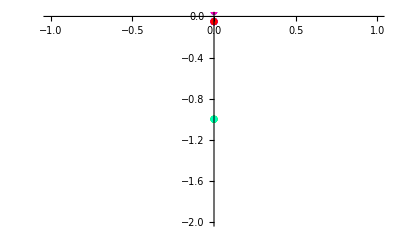

```mathematica
(*Minimization rule*)
Je = 1; (*effective exchange*)
a = 1/100;
δ = 0.1 a ;
hext = 8δ;
hi=hext;
n = 20(*mag field steps*)

(*Satoru's data*)
straintens = a{0.150,0.061,0.041,0.021,.001,-0.019,-0.060,-0.070,-0.080,-0.100,-0.110,-0.12,-0.131,-0.14,-0.160,-0.180,-0.22,-0.261,-0.301};

lmax = Length[straintens];

plotmat = Table[i,{i,n},{j,2}];(*plots k order parameter*)

plots1 = Table[0,{i,lmax}];(*each plot is a different strain*)

hue=Table[{0.3+0.7((l-1)/(lmax-1))},{l,1,lmax}]; (* colors for individual plots*)

For[j = 1,j≤ Length[straintens],j++,
ϵ = straintens[[j]];
η = ϵ/10;
h =  hi;
start = 0;

For[i = 1, i≤ n,i++,
v = NMinimize[f,ψk,Method->"RandomSearch"];(*only care about mx*)
start = v[[2,1,2]];(*solution for ψk*)
plotmat[[i,2]]=-Cos[v[[2,1,2]]];(*Hall Subscript[K, x]*)
plotmat[[i,1]]=h Cos[ψh];(*Subscript[H, x]*)
h = hi-(((2 hi)/n)i);
];

 p1 = ListPlot[plotmat,PlotStyle->{Hue[hue[[j]]]}];
plots1[[j]] = p1;
Clear[ϵ];
Clear[h];
Clear[η];
Clear[start];
]
Show[plots1]
```

```mathematica
v = NMinimize[x^4-3x^2-x,x]
v[[2,1,2]]
```

{-3.51391,{x→1.30084}}

1.30084